### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs=FromReducedRankIndex[642296934875]
```

<|Index→642296934875,QCode→24344244342242333,RuleSet→{A→BC,CB→A,B→AAAA}|>

We generate the sessie and its causal network, again giving it a convenient name:

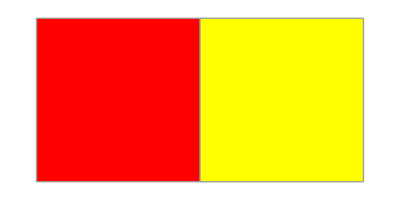
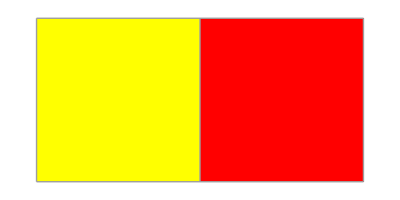

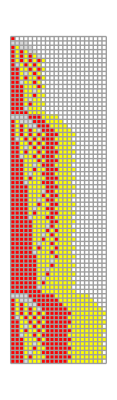
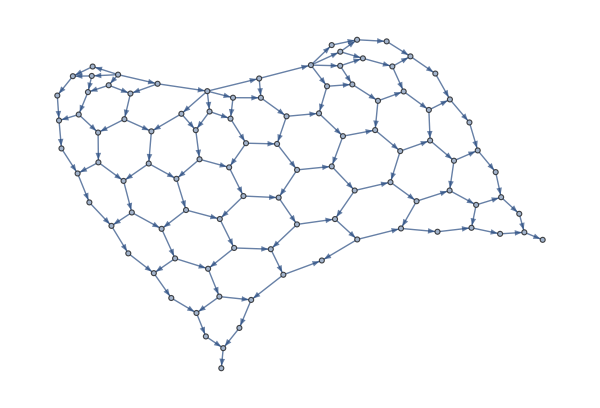
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss=SSS[rs[["RuleSet"]], "B",1000, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss[["Net"]]//Short
```

{1→2,1→3,1→4,1→5,2→6,3→6,6→7,3→8,4→8,8→9,7→10,«1456»,792→994,994→995,989→996,995→996,996→997,991→998,997→998,998→999,993→1000,999→1000}

```mathematica
nds=ToNetDifferenceSets[sss[["Net"]]]
```

{{1,2,3,4},{4,16},{3,5},{4,8},{7},{1},{3,28},{1},{1,5},{1},{5,32},{1},{1},{1},{1},{1},{34},{1,2,3,4},{4,40},{3,5},{4,8},{7,13},{1},{3,52},{1},{1,5},{1},{5,56},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1},{1},{1},{1},{1},{1},{58},{1,2,3,4},{4,64},{3,5},{4,8},{7,13},{1},{3,76},{1},{1,5},{1},{5,80},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1},{1},{1},{1},{1},{1},{82},{1,2,3,4},{4,88},{3,5},{4,8},{7,13},{1},{3,100},{1},{1,5},{1},{5,104},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1},{1},{1},{1},{1},{1},{106},{1,2,3,4},{4,112},{3,5},{4,8},{7,13},{1},{3,124},{1},{1,5},{1},{5,128},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1},{1},{1},{1},{1},{1},{130},{1,2,3,4},{4,136},{3,5},{4,8},{7,13},{1},{3,148},{1},{1,5},{1},{5,152},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1},{1},{1},{1},{1},{1},{154},{1,2,3,4},{4,160},{3,5},{4,8},{7,13},{1},{3,172},{1},{1,5},{1},{5,176},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1},{1},{1},{1},{1},{1},{178},{1,2,3,4},{4,184},{3,5},{4,8},{7,13},{1},{3,196},{1},{1,5},{1},{5,200},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,202},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1},{1},{1},{1},{1},{1},{},{1,2,3,4},{4},{3,5},{4,8},{7,13},{1},{3},{1},{1,5},{1},{5},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7},{1},{1},{1},{1},{1},{1}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[nds,200]
```

{{634,2}}

```mathematica
nds[[1;;634]]
```

{{1,2,3,4},{4,16},{3,5},{4,8},{7},{1},{3,28},{1},{1,5},{1},{5,32},{1},{1},{1},{1},{1},{34},{1,2,3,4},{4,40},{3,5},{4,8},{7,13},{1},{3,52},{1},{1,5},{1},{5,56},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,58},{1},{1},{1},{1},{1},{1},{1},{58},{1,2,3,4},{4,64},{3,5},{4,8},{7,13},{1},{3,76},{1},{1,5},{1},{5,80},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,82},{1},{1},{1},{1},{1},{1},{1},{82},{1,2,3,4},{4,88},{3,5},{4,8},{7,13},{1},{3,100},{1},{1,5},{1},{5,104},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,106},{1},{1},{1},{1},{1},{1},{1},{106},{1,2,3,4},{4,112},{3,5},{4,8},{7,13},{1},{3,124},{1},{1,5},{1},{5,128},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,130},{1},{1},{1},{1},{1},{1},{1},{130},{1,2,3,4},{4,136},{3,5},{4,8},{7,13},{1},{3,148},{1},{1,5},{1},{5,152},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,154},{1},{1},{1},{1},{1},{1},{1},{154},{1,2,3,4},{4,160},{3,5},{4,8},{7,13},{1},{3,172},{1},{1,5},{1},{5,176},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1,7},{1},{1,7},{1},{1,7},{1},{7,178},{1},{1},{1},{1},{1},{1},{1},{178},{1,2,3,4},{4,184},{3,5},{4,8},{7,13},{1},{3,196},{1},{1,5},{1},{5,200}}

Try the reduction:

```mathematica
rsl=ReduceSetList[nds[[1;;634]]]
```

```mathematica
{{1,2,3,4},{4,16},{3,5},{4,8},{7},{1},{3,28},{1},{1,5},{1},{5,32},
€^5[{1}],{34},{1,2,3,4},{4,40},{3,5},{4,8},{7,13},{1},{3,52},{1},{1,5},{1},{5,56},
€^2[{1},{1,7}],
€^2[{1},{7,58},€^3[{1},{1,7}]],{1},{7,58},
€^7[{1}],{58},{1,2,3,4},{4,64},{3,5},{4,8},{7,13},{1},{3,76},{1},{1,5},{1},{5,80},
€^2[{1},{1,7}],

€^5[{1},{7,82},€^3[{1},{1,7}]],{1},{7,82},€^7[{1}],{82},{1,2,3,4},{4,88},{3,5},{4,8},{7,13},{1},{3,100},{1},{1,5},{1},{5,104},€^2[{1},{1,7}],

€^8[{1},{7,106},€^3[{1},{1,7}]],{1},{7,106},€^7[{1}],{106},{1,2,3,4},{4,112},{3,5},{4,8},{7,13},{1},{3,124},{1},{1,5},{1},{5,128},€^2[{1},{1,7}],

€^11[{1},{7,130},€^3[{1},{1,7}]],{1},{7,130},€^7[{1}],{130},{1,2,3,4},{4,136},{3,5},{4,8},{7,13},{1},{3,148},{1},{1,5},{1},{5,152},€^2[{1},{1,7}],

€^14[{1},{7,154},€^3[{1},{1,7}]],{1},{7,154},€^7[{1}],{154},{1,2,3,4},{4,160},{3,5},{4,8},{7,13},{1},{3,172},{1},{1,5},{1},{5,176},€^2[{1},{1,7}],

€^17[{1},{7,178},€^3[{1},{1,7}]],{1},{7,178},€^7[{1}],{178},{1,2,3,4},{4,184},{3,5},{4,8},{7,13},{1},{3,196},{1},{1,5},{1},{5,200}}
```

Not a great success. Try by hand.

```mathematica
rsl[[8]]
```

€_(n$3⊨1)^3[€_(n$1⊨1)^2[{3-3 n$1-6 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{1,-2+n$2+3 n$3},€_(n$1⊨1)^(-4+n$2+3 n$3)[{1,-3+n$1+n$2+3 n$3,-2+n$1+n$2+3 n$3}],{-6+2 n$2+6 n$3,-5+2 n$2+6 n$3,-4+2 n$2+6 n$3},€_(n$1⊨1)^(-1+3 n$3)[€^2[{-3-n$1+2 n$2+6 n$3}]]],€_(n$1⊨1)^2[{1-6 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{1,-1+n$2+3 n$3},€_(n$1⊨1)^(-3+n$2+3 n$3)[{1,-2+n$1+n$2+3 n$3,-1+n$1+n$2+3 n$3}],{-4+2 n$2+6 n$3,-3+2 n$2+6 n$3,-2+2 n$2+6 n$3},€_(n$1⊨1)^(3 n$3)[€^2[{-1-n$1+2 n$2+6 n$3}]]],€_(n$1⊨1)^2[{-1+3 n$1-6 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{1,n$2+3 n$3},€_(n$1⊨1)^(-2+n$2+3 n$3)[{1,-1+n$1+n$2+3 n$3,n$1+n$2+3 n$3}],{-2+2 n$2+6 n$3,-1+2 n$2+6 n$3,2 n$2+6 n$3},€_(n$1⊨1)^(1+3 n$3)[€^2[{1-n$1+2 n$2+6 n$3}]]]]

```mathematica
rsl[[8]] /. {n$1->i, n$2->j, n$3->k}
```

```mathematica
€_(k⊨1)^3[
€_(i⊨1)^2[{9 k i-3 i-6 k+3}],
€_(j⊨1)^2[{1,j+3 k-2},€_(i⊨1)^(j+3 k-4)[{1,i+j+3 k-3,i+j+3 k-2}],{2 j+6 k-6,2 j+6 k-5,2 j+6 k-4},€_(i⊨1)^(3 k-1)[€^2[{-i+2 j+6 k-3}]]],
€_(i⊨1)^2[{9 i k-6 k+1}],
€_(j⊨1)^2[{1,j+3 k-1},€_(i⊨1)^(j+3 k-3)[{1,i+j+3 k-2,i+j+3 k-1}],{2 j+6 k-4,2 j+6 k-3,2 j+6 k-2},€_(i⊨1)^(3 k)[€^2[{-i+2 j+6 k-1}]]],
€_(i⊨1)^2[{9 k i+3 i-6 k-1}],
€_(j⊨1)^2[{1,j+3 k},€_(i⊨1)^(j+3 k-2)[{1,i+j+3 k-1,i+j+3 k}],{2 j+6 k-2,2 j+6 k-1,2 j+6 k},€_(i⊨1)^(3 k+1)[€^2[{-i+2 j+6 k+1}]]]]
```

```mathematica
rsl[[8]] /. {n$1->i, n$2->j, n$3->k}//InputForm
```

IndexedConcatenate[IndexedConcatenate[{3 - 3*i - 6*k + 9*i*k}, {i, 1, 2}], IndexedConcatenate[{1, -2 + j + 3*k}, 
  IndexedConcatenate[{1, -3 + i + j + 3*k, -2 + i + j + 3*k}, {i, 1, -4 + j + 3*k}], {-6 + 2*j + 6*k, -5 + 2*j + 6*k, -4 + 2*j + 6*k}, 
  IndexedConcatenate[IndexedConcatenate[{-3 - i + 2*j + 6*k}, 2], {i, 1, -1 + 3*k}], {j, 1, 2}], 
 IndexedConcatenate[{1 - 6*k + 9*i*k}, {i, 1, 2}], IndexedConcatenate[{1, -1 + j + 3*k}, 
  IndexedConcatenate[{1, -2 + i + j + 3*k, -1 + i + j + 3*k}, {i, 1, -3 + j + 3*k}], {-4 + 2*j + 6*k, -3 + 2*j + 6*k, -2 + 2*j + 6*k}, 
  IndexedConcatenate[IndexedConcatenate[{-1 - i + 2*j + 6*k}, 2], {i, 1, 3*k}], {j, 1, 2}], 
 IndexedConcatenate[{-1 + 3*i - 6*k + 9*i*k}, {i, 1, 2}], IndexedConcatenate[{1, j + 3*k}, 
  IndexedConcatenate[{1, -1 + i + j + 3*k, i + j + 3*k}, {i, 1, -2 + j + 3*k}], {-2 + 2*j + 6*k, -1 + 2*j + 6*k, 2*j + 6*k}, 
  IndexedConcatenate[IndexedConcatenate[{1 - i + 2*j + 6*k}, 2], {i, 1, 1 + 3*k}], {j, 1, 2}], {k, 1, 3}]

Can we do better?

```mathematica
{ExpandAll[%]}
```

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```